H ΕΝΝΟΙΑ ΤΗΣ ΠΑΡΑΓΩΓΟΥ

Ορισμός 
Μια συνάρτηση f λέμε ότι είναι παραγωγίσιμη σ’ ένα σημείο x_0 του πεδίου ορισμού της, αν υπάρχει το  
                                                                                                                                                                  
					lim_(x→ x_0) (f(x)- f(x_0))/(x-x_0)                                                              
και είναι πραγματικός αριθμός.                                                                                                                  
Το όριο αυτό ονομάζεται παράγωγος της f στο x_0 και συμβολίζεται με f ʹ(x_0). Δηλαδή:                             
                                                                  f ʹ(x_0)= lim_(x→ x_0) (f(x)- f(x_0))/(x-x_0)

Ορισμός 
Έστω f μια συνάρτηση και  Α(x_0, f(x_0))  ένα σημείο της  C_f.                                                                    
Αν υπάρχει το  lim_(x→ x_0) (f(x)- f(x_0))/(x-x_0)   και είναι ένας πραγματικός αριθμός λ,                                            
τότε ορίζουμε ως εφαπτομένη της Cf στο σημείο της Α, την ευθεία ε που διέρχεται από το Α                 
και έχει συντελεστή διεύθυνσης λ.                                                                                                           

Επομένως, η εξίσωση της εφαπτομένης στο σημείο Α(x_0, f(x_0))  είναι:
			                     y−f(x_0)=λ (x−x_0)

όπως ορίσαμε παραπάνω λ = f ʹ(x_0)  οπότε η εξίσωση εφαπτομένης στο σημείο Α είναι:

                                           y−f(x_0)=f'(x_0) (x−x_0)

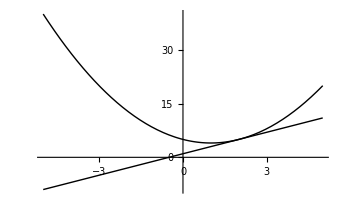
Συμπέρασματα : 
Έστω f(x) μια συνάρτηση και  ε  η εξίσωση της εφαπτομένης της C_f στο σημείο x_0  με x_0∈ D_f. Ισχύουν τα παρακάτω:

	☑  Η τιμή f'(x_0) είναι η κλίση της εφαπτομένης ε
	☑  Η τιμή f'(x_0) ισούται με την εφαπτομένη της γωνίας που σχηματίζει η ευθεία ε με τον άξονα xx’
	☑  Όταν  f'(x_0)=0  η ευθεία ε είναι παράλληλη στον άξονα  xx’
	☑  Όταν  f'(x_0)<0  η ευθεία ε σχηματίζει αβλεία γωνία με τον άξονα  xx’
	☑  Όταν  f'(x_0)>0  η ευθεία ε σχηματίζει οξεία γωνία με τον άξονα  xx’




💡  Παράδειγμα 
Έστω η συνάρτηση f(x)= x^2 -2x + 5 . Ψάχνουμε την εξίσωση εφαπτομένης της C_f στο σημείο x_0=2

✓   Λύση  :

	Υπολογίζουμε την τιμή  f ʹ(2) :

		•  Υπολογισμός με τον ορισμό παραγώγου σε σημείο
	  
		  f'(2)= lim_(x→ 2) (f(x)- f(2))/(x-2)= lim_(x→ 2) (x^2 -2x)/(x-2) =lim_(x→ 2) (x (x -2))/(x -2)= 2 
	
		•  Υπολογισμός με κανόνες παραγώγισης:  f ’(x)= 2x -2     ,   f ʹ(2)=2
	
	Βρίσκουμε την εξίσωση εφαπτομένης:    

	y - f(2) = f ’(2) ( x - 2 )     ⟺     y - 5 = 2 ( x - 2 )      ⟺
		
	ε :  y = 2 x  + 1                  

	Παρακάτω βλέπουμε την γραφική παράσταση της συνάρτησης και της ευθείας ε.

	-Graphics-

💡  Παράδειγμα με την βοήθεια του Mathematica 

Το παρακάτω πρόγραμμα υπολογίζει την εξίσωση εφαπτομένης με τον τρόπο που υπολογίστηκε στο παραπάνω παράδειγμα.
Στη συνέχεια παρουσιάζει στο ίδιο σύστημα αξόνων τις γραφικές παραστάσεις της συνάρτησης και της εφαπτομένης.

⚠  Για να τρέξεις το πρόγραμμα πάτησε Shift + Enter σε οποιαδήποτε γραμμή του παρακάτω κώδικα.

✓  Σείρε την μπάρα για να αλλάξεις το σημείο x_0

✓  Μπορείς να επιλέξεις διάφορες συναρτήσεις.

☺  Μπορείς να επαληθεύσεις με πράξεις την εξίσωση της εφαπτομένης για ορισμένες τιμές.

```mathematica
Clear["Global`*"]
f1[x_]:=x^2;f2[x_]:=3x-x^2+2;f3[x_]:=x^3;f4[x_]:=Sin[x]-x;f5[x_]:=Sin[x]-x^2+2*x;f6[x_]:= Log[x^2+2];f7[x_]:=Sin[x]-1/5*x +1/10 *x^2

(*το διάστημα (-L,L) που μπορεί να πάρει τιμές το x*)
L=7;

Panel[Style[Manipulate[Grid[{  {Grid[ {{"▸ f(x_0)   =" ,f[x0]}}]},{Grid[ {{"▸ f'(x_0)  =",f'[x0]}}]},{Grid[ {{"▸ Εξίσωση εφαπτομένης στο x_0 :    y = ",f'[x0]*x-x0+f[x0]}}]},{Show[{Plot[f[x],{x,-L,L},AxesLabel->{"x","y"},PlotRange->Automatic,PlotLegends->{"f(x)"},Background->White,PlotStyle->{Black,Thick},Epilog->{ Blue,Opacity[0.8],PointSize[0.009],Point[{x0,f[x0]}]   }],
Plot[f[x0]+f'[x0](x-x0),{x,-L,L},PlotLegends->{"Εξ. Εφ."},PlotStyle->{Red}]},ImageSize->{600,450}
], }},Alignment->{Left}]
,{{x0,-L,"Σημείο x_0"},-L,L,0.1,Appearance->"Labeled"},{{f,f,"Συνάρτηση: "},{f1->" x^2 ",f2->" 3x-x^2+2 ",f3->" x^3 ",f4->" ημ(x)-x ",f5->" ημ(x)-x^2+2x ",f6->" ln(x^2+2) ",f7->" ημ(x)+x^2/10-x/5"}}
],DefaultOptions->{Panel->{Background->LightBlue}}],FrameMargins->{{-3,-2},{-2,-3}}]
```